```mathematica
(*
e[x]_here = e_1(x)_{Lagrangian approach};
v[x]_here = {v^1(x)}_{Lagrangian approach};
σ[x]_here  = σ(x)_{Lagrangian approach};
*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ϵ[1]=1;
```

```mathematica
ass={ψ[x]∈Reals,ν[x]>0};
```

```mathematica
e[x_]:=ν[x]{Cos[ψ[x]],-Sin[ψ[x]]}
```

```mathematica
n[x_]:={-e[x][[2]],e[x][[1]]}/Norm[e[x]]
```

```mathematica
g[x_]:=Simplify[{{e[x].e[x]}},Assumptions->ass]
```

```mathematica
sqrtdetg[x_]:=Sqrt[Det[g[x]]]
```

```mathematica
gc[x_]:=Inverse[g[x]]
```

```mathematica
FullSimplify[{{-n'[x].e[x]}},Assumptions->ass]
```

{{-ν[x] ψ'[x]}}

```mathematica
b[x_]:={{-ν[x] ψ'[x]}}
```

```mathematica
1/2FullSimplify[Sum[gc[x][[i,j]]b[x][[j,i]],{i,1,1},{j,1,1}],Assumptions->ass]
```

-ψ'[x]/(2 ν[x])

```mathematica
H[x_]:=-ψ'[x]/(2 ν[x])
```

```mathematica
K[x_]:=0
```

```mathematica
Γ[x_]:=ResourceFunction["ChristoffelSymbol"][g[x],{x}] //FullSimplify
```

```mathematica
Γ[x]
```

{{{ν'[x]/ν[x]}}}

```mathematica
(* \Nabla_k f_i*)
```

```mathematica
Nablaf[f_][i_,k_][x_]:=Derivative[ϵ[k]][f[i]][x]-Sum[f[j][x] Γ[x][[j,i,k]],{j,1,1}]
```

```mathematica
(*\Nabla_k v^i*)
```

```mathematica
Nablav[v_][i_,k_][x_]:=Derivative[ϵ[k]][v[i]][x]+Sum[v[j][x] Γ[x][[i,j,k]],{j,1,1}]
```

```mathematica
(*Nabla_k t^{il}*)
```

```mathematica
Nablavv[t_][i_,l_,k_][x_]:=Derivative[ϵ[k]][t[i,l]][x]+Sum[t[j,l][x] Γ[x][[i,j,k]],{j,1,1}]+Sum[t[i,j][x] Γ[x][[l,j,k]],{j,1,1}]
```

```mathematica
dH[1][x_]:=H'[x]
```

```mathematica
(*expression for Nabla_i Nabla^i H*)
```

```mathematica
FullSimplify[Sum[gc[x][[i,j]]Nablaf[dH][i,j][x],{i,1,1},{j,1,1}],Assumptions->ass]
```

(-3 ν'[x]^2 ψ'[x]+3 ν[x] ν'[x] ψ''[x]+ν[x] (ψ'[x] ν''[x]-ν[x] ψ^(3)[x]))/(2 ν[x]^5)

```mathematica
NabNabH[x_]:=(-3 ν'[x]^2 ψ'[x]+3 ν[x] ν'[x] ψ''[x]+ν[x] (ψ'[x] ν''[x]-ν[x] Derivative[3][ψ][x]))/(2 ν[x]^5)
```

```mathematica
(*auxiliary definition to obtain the covariant derivatives of v*)
```

```mathematica
vv[1][x_]:=v[x]
```

```mathematica
FullSimplify[Nablav[vv][1,1][x],Assumptions->ass]
```

v'[x]+(v[x] ν'[x])/ν[x]

```mathematica
(*Nablaivi = Nabla_i v^i*)
```

```mathematica
Nablaivi[x_]:=FullSimplify[Nablav[vv][1,1][x],Assumptions->ass]
```

```mathematica
(*rate-of-deformation tensor d^{ij}*)
```

```mathematica
dc[1,1][x_]:=gc[x][[1,1]]Nablav[vv][1,1][x]-w[x]gc[x][[1,1]]gc[x][[1,1]]b[x][[1,1]]
```

```mathematica
eqv=FullSimplify[ρ(v[x]Nablaivi[x]-2 v[x]w[x] gc[x][[1,1]]b[x][[1,1]]-w[x] gc[x][[1,1]]w'[x])
-gc[x][[1,1]]σ'[x]-2 η Nablavv[dc][1,1,1][x]==0,Assumptions->ass];
eqσ=FullSimplify[Nablaivi[x]-2 H[x]w[x]==0,Assumptions->ass];
eqψ=FullSimplify[{ρ v[x](v[x]b[x][[1,1]]+w'[x])
-κ( - 2 NabNabH[x]-4H[x](H[x]^2-K[x]))
-2 σ[x]H[x]
- 2η( Nablaivi[x] gc[x][[1,1]]b[x][[1,1]]-2 w[x]*(2 H[x]^2-K[x]))==0},Assumptions->ass];
eqX={X1'[x]==ν[x] Cos[ψ[x]],X2'[x]==-ν[x] Sin[ψ[x]]};
```

```mathematica
eqv
```

v[x] (ρ ν[x]^4 v'[x]+2 η ν'[x]^2+ρ ν[x]^3 (v[x] ν'[x]+2 w[x] ψ'[x])-2 η ν[x] ν''[x])==ν[x] (ν[x] σ'[x]+2 η (v'[x] ν'[x]+w'[x] ψ'[x]+ν[x] v''[x]))+w[x] (ρ ν[x]^2 w'[x]-2 η ν'[x] ψ'[x]+2 η ν[x] ψ''[x])

```mathematica
(* given that I am at steady state, it must be w[x]=0, thus I simplify the equations by setting *)
```

```mathematica
w[x_]:=0
```

```mathematica
eqσ
```

ν[x] v'[x]+v[x] ν'[x]==0

```mathematica
(*
eqσ implies that ν[x] * v[x] = const., thus  

v[x]=A/ν[x];
  v[xmin]=A/ν[xmin];
  A= v[xmin] * ν[xmin];
thus
v[x]=v[xmin] * ν[xmin]/ν[x]
*)
```

```mathematica
repv={v[x]->A/ν[x],v'[x]->-(A ν'[x])/ν[x]^2,v''[x]->(A (2 ν'[x]^2-ν[x] ν''[x]))/ν[x]^3};
```

```mathematica
FullSimplify[eqv/.repv]
```

ν[x] σ'[x]==0

```mathematica
(*eqv thus implies that σ[x]= σc*)
```

```mathematica
σ[x_]:=σc
```

```mathematica
(*fix the gauge*)
```

```mathematica
ν[x_]:=νc
```

```mathematica
(*we thus reduce the original problem for v,w,σ,ψ,X to a reduced problem for ψ and X only*)
```

```mathematica
(*the boundary conditions and differential equations for the reduced problem are*)
```

```mathematica
bcs={
ψ[xmin]==ψmin,ψ[xmax]==ψmax,
X1[xmin]==X1min,X2[xmin]==X2min,X1[xmax]==X1max};
```

```mathematica
eqs=Flatten[{eqψ,eqX}/.repv]
```

{2 A^2 νc^4 ρ ψ'[x]+κ νc^2 ψ'[x]^3+2 κ νc^2 ψ^(3)[x]==0,X1'[x]==νc Cos[ψ[x]],X2'[x]==-νc Sin[ψ[x]]}

```mathematica
(*parameters*)
```

```mathematica
κ=1;
ρ=1;
η=1;
xmin=0;
xmax=1;
vmin=1;
A=vmin*ν[xmin];
σc=1;
νc=1.2;
ψmin=0;
ψmax=0;
X1min=0;
X2min=0;
X1max=1;
```

```mathematica
(*this is the value of v_r to be instered into the variational problem *)
```

```mathematica
v[x]/.repv/.{x->xmax}
```

1.

```mathematica
s=NDSolve[FullSimplify[Flatten[{eqs,bcs}]],{ψ,X1,X2},{x,xmin,xmax}][[1]]
```

{ψ→InterpolatingFunction[…],X1→InterpolatingFunction[…],X2→InterpolatingFunction[…]}

```mathematica
(*this is the value of X2r to be entered into the variational problem*)
N[Rationalize[X2[xmax]/.s,0],30]
```

-0.595581754438050373465988519156

```mathematica
NotebookEvaluate["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/ode_on_mesh.nb"]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/nu.csv

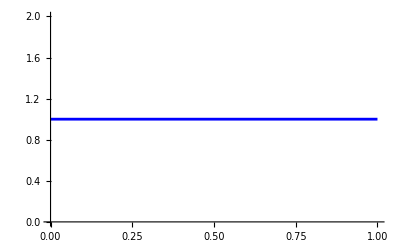

```mathematica
plotvexact=Plot[v[x]/.repv/.s,{x,xmin,xmax},PlotStyle->Blue]
```

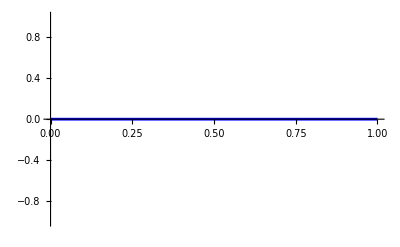

```mathematica
plotwexact=Plot[w[x],{x,xmin,xmax},PlotStyle->Blue]
```

```mathematica
plotσexact=Plot[σ[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

-Graphics-

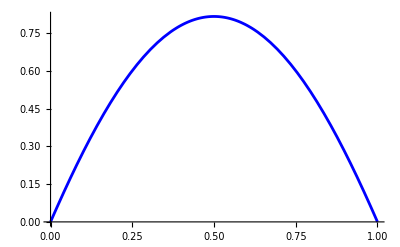

```mathematica
plotψexact=Plot[ψ[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

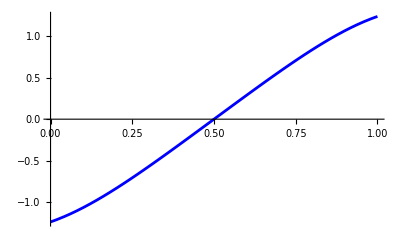

```mathematica
plotμexact=Plot[H[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

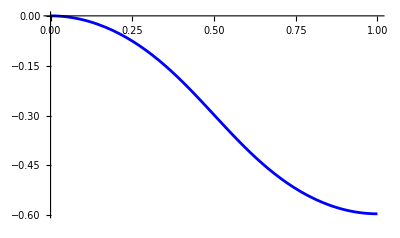

```mathematica
plotXexact=ParametricPlot[{X1[x],X2[x]}/.s,{x,xmin,xmax},PlotStyle->Blue]
```

```mathematica
(*check FE solution*)
```

```mathematica
(*check v*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/v.csv"];
t=Table[{t[[i,4]],t[[i,1]]},{i,2,Length[t]}]
```

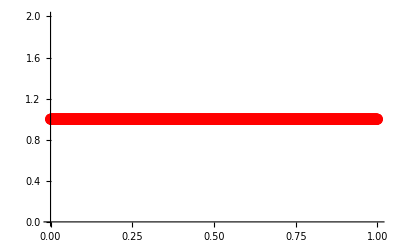

```mathematica
plotvnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

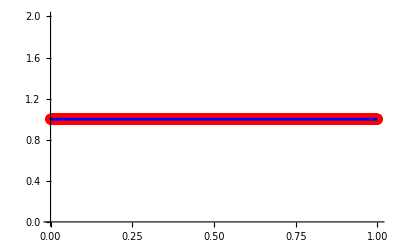

```mathematica
Show[plotvnum,plotvexact]
```

```mathematica
(*check w*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/w.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

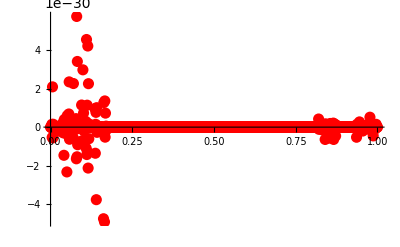

```mathematica
plotwnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

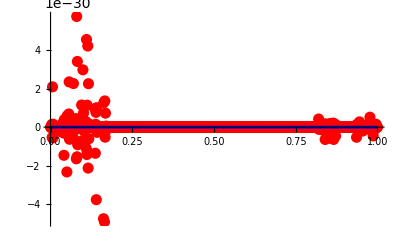

```mathematica
Show[plotwnum,plotwexact]
```

```mathematica
(*check sigma*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/sigma.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

```mathematica
plotσnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

-Graphics-

```mathematica
Show[plotσnum,plotσexact]
```

-Graphics-

```mathematica
(*check ψ*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/psi.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

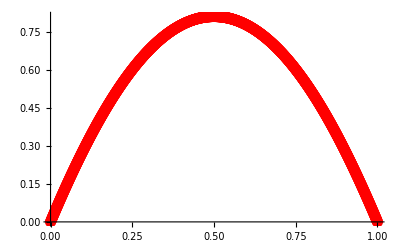

```mathematica
plotψnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

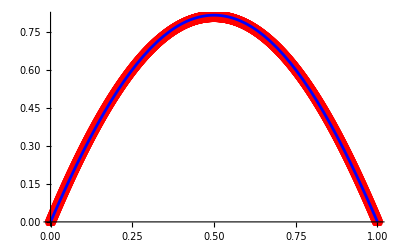

```mathematica
Show[plotψnum,plotψexact]
```

```mathematica
(*check μ*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/mu.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

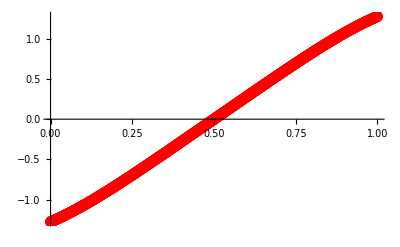

```mathematica
plotμnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

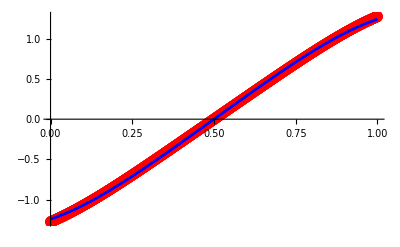

```mathematica
Show[plotμnum,plotμexact]
```

```mathematica
(*check X*)
```

```mathematica
tX=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/X.csv"];
tX=Table[{tX[[i,1]],tX[[i,2]]},{i,2,Length[tX]}]
```

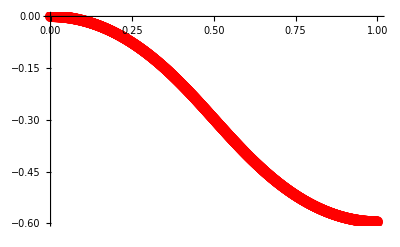

```mathematica
plotXnum=ListPlot[tX,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

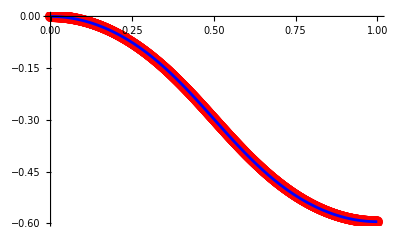

```mathematica
Show[plotXnum,plotXexact]
```